## Function to return cellular automata properties

```mathematica
PercentageYell [cellist_]:= Count[cellist,0]÷ Length @ cellist*100.;
```

```mathematica
trialcell = Flatten[CellularAutomaton[{69,3},RandomChoice[{.7,.2, .1}-> {0,1,2}, 120],30]];
```

```mathematica
Count[trialcell,0]÷ Length @ trialcell * 100.
```

79.5699

```mathematica
PercentageYell[Flatten[CellularAutomaton[{69,3},RandomChoice[{.7,.2, .1}-> {0,1,2}, 120],30]]]
```

79.4624

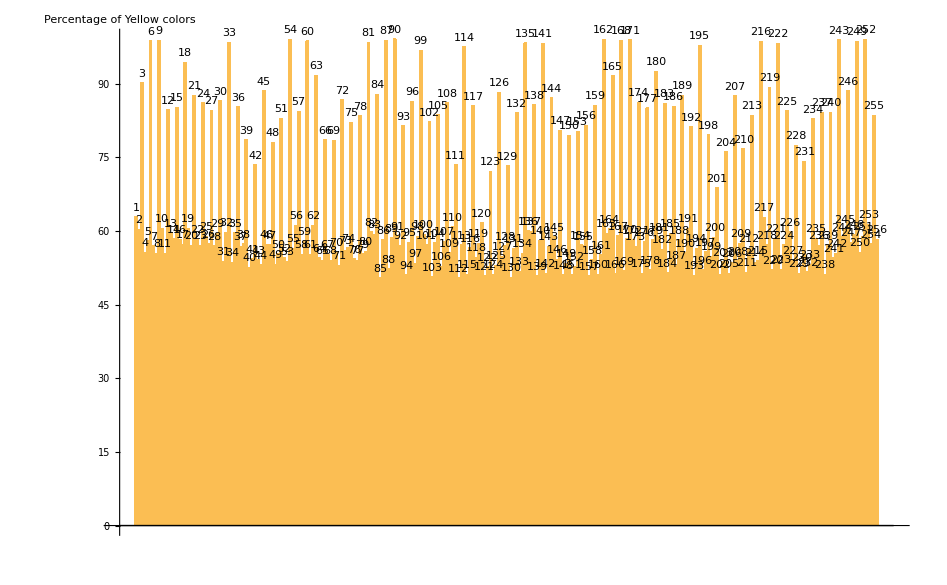

```mathematica
BarChart[Table[PercentageYell[Flatten[CellularAutomaton[{rulnum,3},RandomChoice[{.7,.2, .1}-> {0,1,2}, 120],30]]],{rulnum,1,256}], AxesLabel-> "Percentage of Yellow colors", ChartLabels-> {Placed[Range[256],Above]}]
```

## Systematic investigation of rules

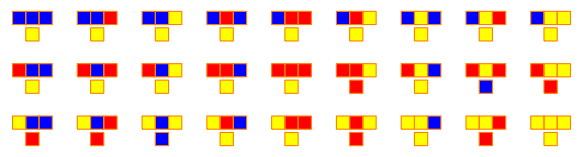

```mathematica
rulplot=RulePlot[CellularAutomaton[{679458,3}],ColorRules->{0->Yellow,1->Red,2->Blue},MeshStyle->Orange]
```

```mathematica
Length @ Flatten[CellularAutomaton[{69,3},RandomChoice[{.7,.2, .1}-> {0,1,2}, 120],30]]
```

3720

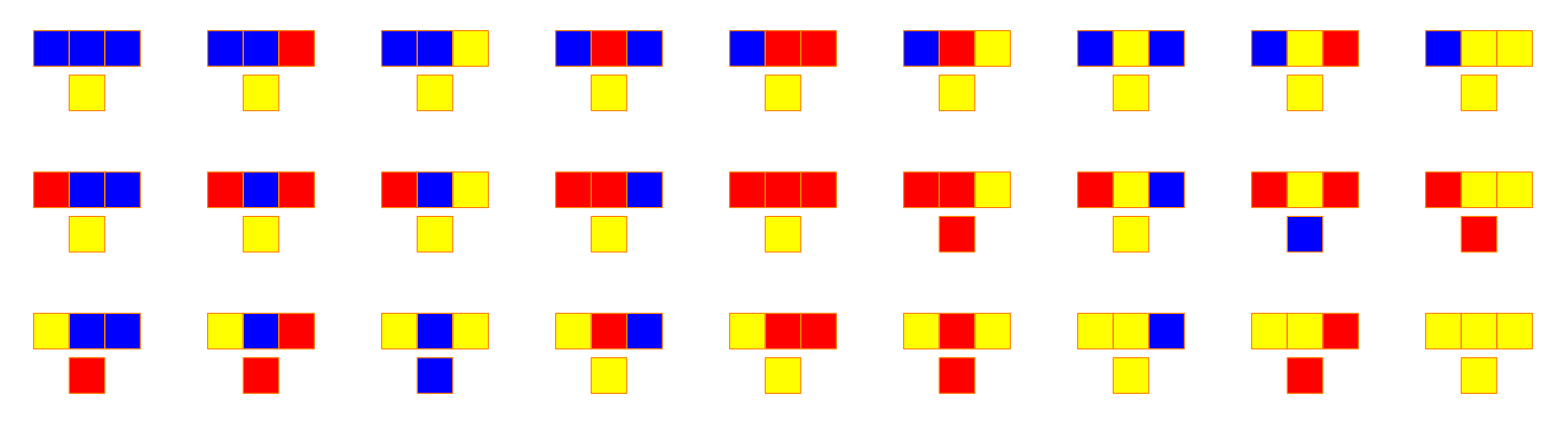

```mathematica
Show[rulplot,ImageSize->Full]
```

Trying  1 to 700000?

```mathematica
Quiet[Integer[rulenum]^=True;]
colornum = 3;
Quiet[Integer[colornum]^=True;]
RulPlt[rulenum_]:=RulePlot[CellularAutomaton[{rulenum,3}],ColorRules->{0->Yellow,1->Red,2->Blue},MeshStyle->Orange, ImageSize -> Full];
RuleLoop[rulenum_]:= BlockRandom[SeedRandom[1000];
ArrayPlot[CellularAutomaton[{rulenum,colornum},RandomChoice[{.7,.2, .1}-> {0,1,2}, 120],30],Mesh->True,ColorRules->{0->Yellow,1->Red, 2-> Blue},MeshStyle->Orange, ImageSize ->  Full]];
```

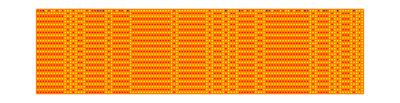
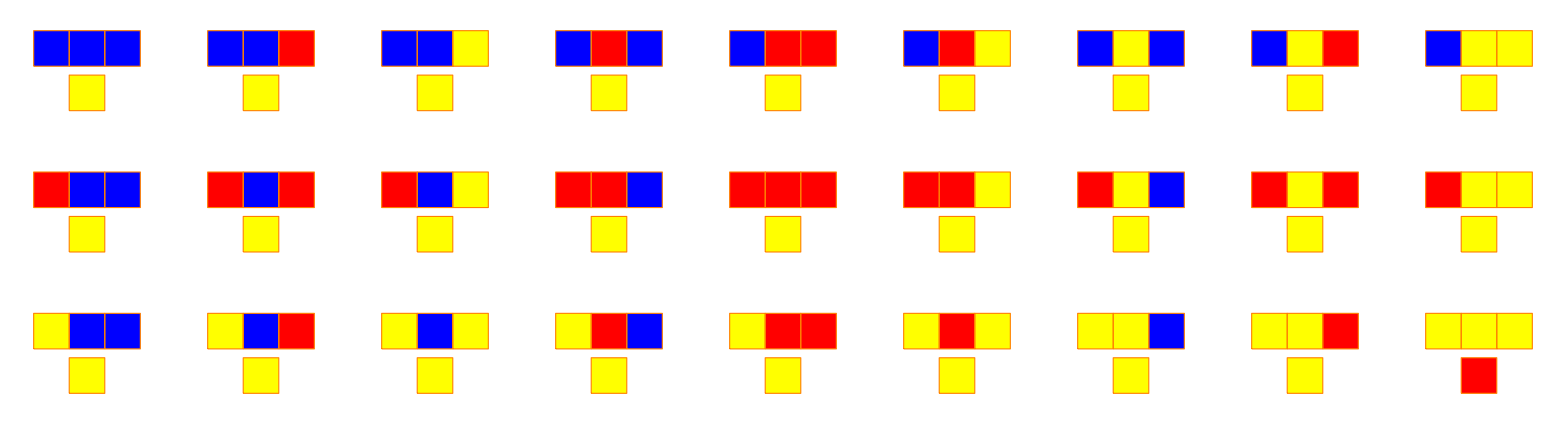
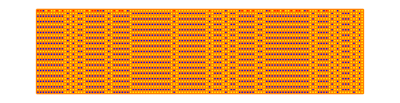
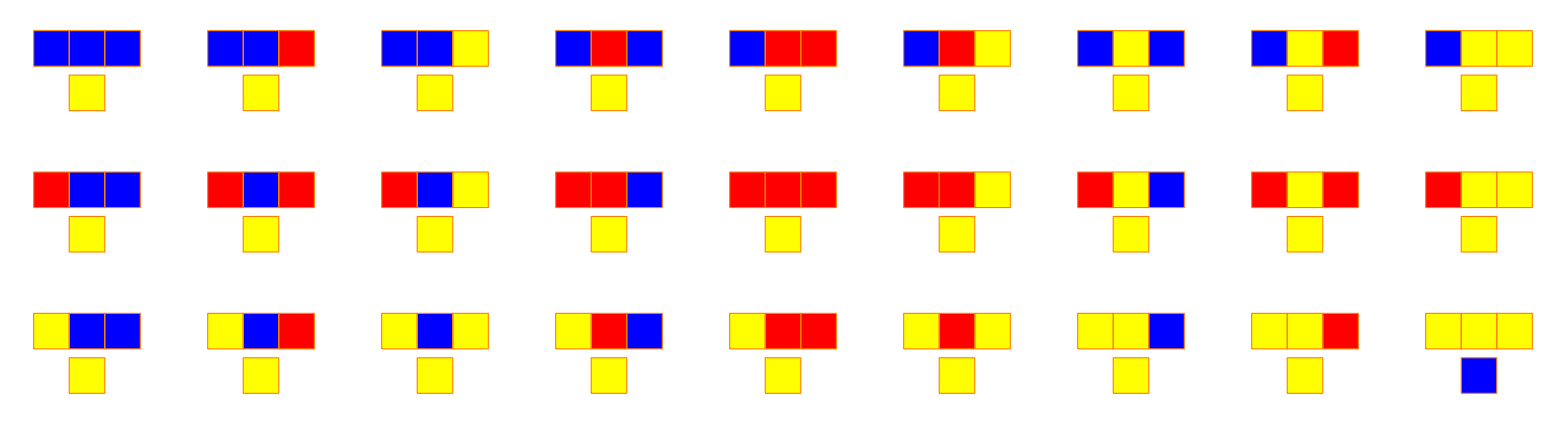
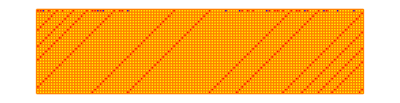
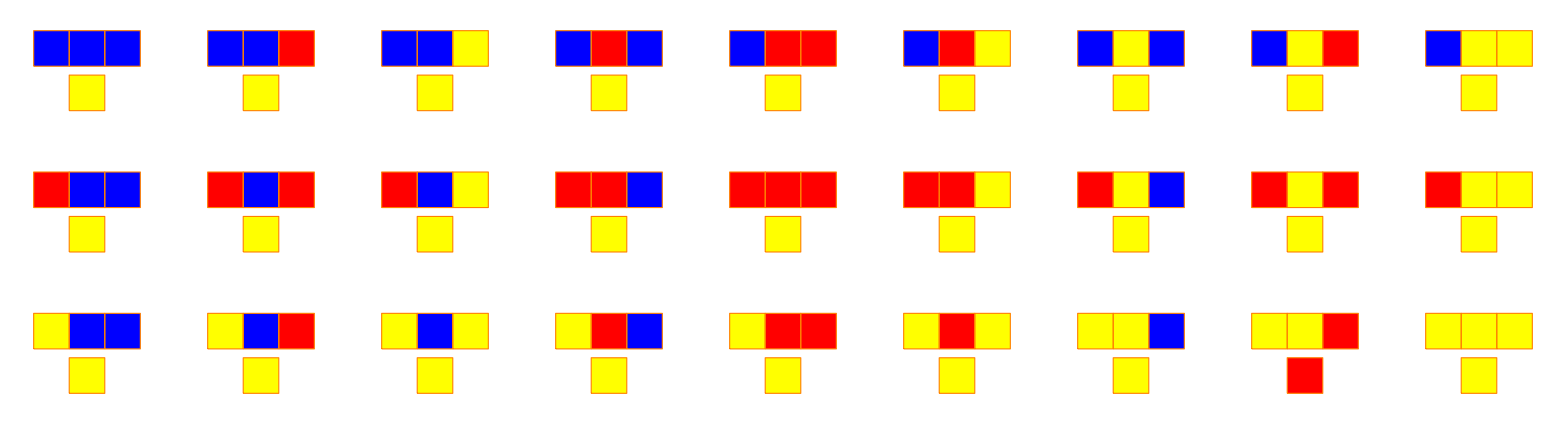
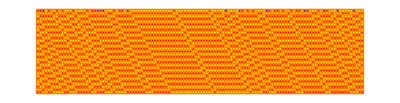
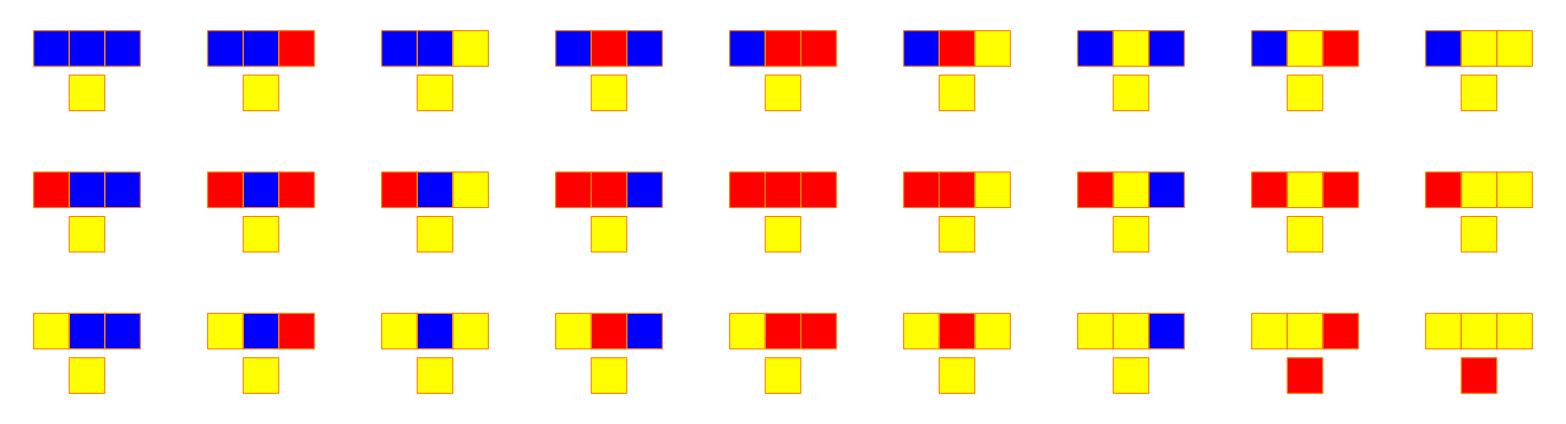
1 | -Graphics- | -Graphics-
2 | -Graphics- | -Graphics-
3 | -Graphics- | -Graphics-
4 | -Graphics- | -Graphics-
5 | -Graphics- | -Graphics-
6 | -Graphics- | -Graphics-
7 | -Graphics- | -Graphics-
8 | -Graphics- | -Graphics-
9 | -Graphics- | -Graphics-
10 | -Graphics- | -Graphics-
11 | -Graphics- | -Graphics-
12 | -Graphics- | -Graphics-
13 | -Graphics- | -Graphics-
14 | -Graphics- | -Graphics-
15 | -Graphics- | -Graphics-
16 | -Graphics- | -Graphics-
17 | -Graphics- | -Graphics-
18 | -Graphics- | -Graphics-
19 | -Graphics- | -Graphics-
20 | -Graphics- | -Graphics-
21 | -Graphics- | -Graphics-
22 | -Graphics- | -Graphics-
23 | -Graphics- | -Graphics-
24 | -Graphics- | -Graphics-
25 | -Graphics- | -Graphics-
26 | -Graphics- | -Graphics-
27 | -Graphics- | -Graphics-
28 | -Graphics- | -Graphics-
29 | -Graphics- | -Graphics-
30 | -Graphics- | -Graphics-
31 | -Graphics- | -Graphics-
32 | -Graphics- | -Graphics-
33 | -Graphics- | -Graphics-
34 | -Graphics- | -Graphics-
35 | -Graphics- | -Graphics-
36 | -Graphics- | -Graphics-
37 | -Graphics- | -Graphics-
38 | -Graphics- | -Graphics-
39 | -Graphics- | -Graphics-
40 | -Graphics- | -Graphics-
41 | -Graphics- | -Graphics-
42 | -Graphics- | -Graphics-
43 | -Graphics- | -Graphics-
44 | -Graphics- | -Graphics-
45 | -Graphics- | -Graphics-
46 | -Graphics- | -Graphics-
47 | -Graphics- | -Graphics-
48 | -Graphics- | -Graphics-
49 | -Graphics- | -Graphics-
50 | -Graphics- | -Graphics-
51 | -Graphics- | -Graphics-
52 | -Graphics- | -Graphics-
53 | -Graphics- | -Graphics-
54 | -Graphics- | -Graphics-
55 | -Graphics- | -Graphics-
56 | -Graphics- | -Graphics-
57 | -Graphics- | -Graphics-
58 | -Graphics- | -Graphics-
59 | -Graphics- | -Graphics-
60 | -Graphics- | -Graphics-
61 | -Graphics- | -Graphics-
62 | -Graphics- | -Graphics-
63 | -Graphics- | -Graphics-
64 | -Graphics- | -Graphics-
65 | -Graphics- | -Graphics-
66 | -Graphics- | -Graphics-
67 | -Graphics- | -Graphics-
68 | -Graphics- | -Graphics-
69 | -Graphics- | -Graphics-
70 | -Graphics- | -Graphics-
71 | -Graphics- | -Graphics-
72 | -Graphics- | -Graphics-
73 | -Graphics- | -Graphics-
74 | -Graphics- | -Graphics-
75 | -Graphics- | -Graphics-
76 | -Graphics- | -Graphics-
77 | -Graphics- | -Graphics-
78 | -Graphics- | -Graphics-
79 | -Graphics- | -Graphics-
80 | -Graphics- | -Graphics-
81 | -Graphics- | -Graphics-
82 | -Graphics- | -Graphics-
83 | -Graphics- | -Graphics-
84 | -Graphics- | -Graphics-
85 | -Graphics- | -Graphics-
86 | -Graphics- | -Graphics-
87 | -Graphics- | -Graphics-
88 | -Graphics- | -Graphics-
89 | -Graphics- | -Graphics-
90 | -Graphics- | -Graphics-
91 | -Graphics- | -Graphics-
92 | -Graphics- | -Graphics-
93 | -Graphics- | -Graphics-
94 | -Graphics- | -Graphics-
95 | -Graphics- | -Graphics-
96 | -Graphics- | -Graphics-
97 | -Graphics- | -Graphics-
98 | -Graphics- | -Graphics-
99 | -Graphics- | -Graphics-
100 | -Graphics- | -Graphics-
101 | -Graphics- | -Graphics-
102 | -Graphics- | -Graphics-
103 | -Graphics- | -Graphics-
104 | -Graphics- | -Graphics-
105 | -Graphics- | -Graphics-
106 | -Graphics- | -Graphics-
107 | -Graphics- | -Graphics-
108 | -Graphics- | -Graphics-
109 | -Graphics- | -Graphics-
110 | -Graphics- | -Graphics-
111 | -Graphics- | -Graphics-
112 | -Graphics- | -Graphics-
113 | -Graphics- | -Graphics-
114 | -Graphics- | -Graphics-
115 | -Graphics- | -Graphics-
116 | -Graphics- | -Graphics-
117 | -Graphics- | -Graphics-
118 | -Graphics- | -Graphics-
119 | -Graphics- | -Graphics-
120 | -Graphics- | -Graphics-
121 | -Graphics- | -Graphics-
122 | -Graphics- | -Graphics-
123 | -Graphics- | -Graphics-
124 | -Graphics- | -Graphics-
125 | -Graphics- | -Graphics-
126 | -Graphics- | -Graphics-
127 | -Graphics- | -Graphics-
128 | -Graphics- | -Graphics-
129 | -Graphics- | -Graphics-
130 | -Graphics- | -Graphics-
131 | -Graphics- | -Graphics-
132 | -Graphics- | -Graphics-
133 | -Graphics- | -Graphics-
134 | -Graphics- | -Graphics-
135 | -Graphics- | -Graphics-
136 | -Graphics- | -Graphics-
137 | -Graphics- | -Graphics-
138 | -Graphics- | -Graphics-
139 | -Graphics- | -Graphics-
140 | -Graphics- | -Graphics-
141 | -Graphics- | -Graphics-
142 | -Graphics- | -Graphics-
143 | -Graphics- | -Graphics-
144 | -Graphics- | -Graphics-
145 | -Graphics- | -Graphics-
146 | -Graphics- | -Graphics-
147 | -Graphics- | -Graphics-
148 | -Graphics- | -Graphics-
149 | -Graphics- | -Graphics-
150 | -Graphics- | -Graphics-
151 | -Graphics- | -Graphics-
152 | -Graphics- | -Graphics-
153 | -Graphics- | -Graphics-
154 | -Graphics- | -Graphics-
155 | -Graphics- | -Graphics-
156 | -Graphics- | -Graphics-
157 | -Graphics- | -Graphics-
158 | -Graphics- | -Graphics-
159 | -Graphics- | -Graphics-
160 | -Graphics- | -Graphics-
161 | -Graphics- | -Graphics-
162 | -Graphics- | -Graphics-
163 | -Graphics- | -Graphics-
164 | -Graphics- | -Graphics-
165 | -Graphics- | -Graphics-
166 | -Graphics- | -Graphics-
167 | -Graphics- | -Graphics-
168 | -Graphics- | -Graphics-
169 | -Graphics- | -Graphics-
170 | -Graphics- | -Graphics-
171 | -Graphics- | -Graphics-
172 | -Graphics- | -Graphics-
173 | -Graphics- | -Graphics-
174 | -Graphics- | -Graphics-
175 | -Graphics- | -Graphics-
176 | -Graphics- | -Graphics-
177 | -Graphics- | -Graphics-
178 | -Graphics- | -Graphics-
179 | -Graphics- | -Graphics-
180 | -Graphics- | -Graphics-
181 | -Graphics- | -Graphics-
182 | -Graphics- | -Graphics-
183 | -Graphics- | -Graphics-
184 | -Graphics- | -Graphics-
185 | -Graphics- | -Graphics-
186 | -Graphics- | -Graphics-
187 | -Graphics- | -Graphics-
188 | -Graphics- | -Graphics-
189 | -Graphics- | -Graphics-
190 | -Graphics- | -Graphics-
191 | -Graphics- | -Graphics-
192 | -Graphics- | -Graphics-
193 | -Graphics- | -Graphics-
194 | -Graphics- | -Graphics-
195 | -Graphics- | -Graphics-
196 | -Graphics- | -Graphics-
197 | -Graphics- | -Graphics-
198 | -Graphics- | -Graphics-
199 | -Graphics- | -Graphics-
200 | -Graphics- | -Graphics-
201 | -Graphics- | -Graphics-
202 | -Graphics- | -Graphics-
203 | -Graphics- | -Graphics-
204 | -Graphics- | -Graphics-
205 | -Graphics- | -Graphics-
206 | -Graphics- | -Graphics-
207 | -Graphics- | -Graphics-
208 | -Graphics- | -Graphics-
209 | -Graphics- | -Graphics-
210 | -Graphics- | -Graphics-
211 | -Graphics- | -Graphics-
212 | -Graphics- | -Graphics-
213 | -Graphics- | -Graphics-
214 | -Graphics- | -Graphics-
215 | -Graphics- | -Graphics-
216 | -Graphics- | -Graphics-
217 | -Graphics- | -Graphics-
218 | -Graphics- | -Graphics-
219 | -Graphics- | -Graphics-
220 | -Graphics- | -Graphics-
221 | -Graphics- | -Graphics-
222 | -Graphics- | -Graphics-
223 | -Graphics- | -Graphics-
224 | -Graphics- | -Graphics-
225 | -Graphics- | -Graphics-
226 | -Graphics- | -Graphics-
227 | -Graphics- | -Graphics-
228 | -Graphics- | -Graphics-
229 | -Graphics- | -Graphics-
230 | -Graphics- | -Graphics-
231 | -Graphics- | -Graphics-
232 | -Graphics- | -Graphics-
233 | -Graphics- | -Graphics-
234 | -Graphics- | -Graphics-
235 | -Graphics- | -Graphics-
236 | -Graphics- | -Graphics-
237 | -Graphics- | -Graphics-
238 | -Graphics- | -Graphics-
239 | -Graphics- | -Graphics-
240 | -Graphics- | -Graphics-
241 | -Graphics- | -Graphics-
242 | -Graphics- | -Graphics-
243 | -Graphics- | -Graphics-
244 | -Graphics- | -Graphics-
245 | -Graphics- | -Graphics-
246 | -Graphics- | -Graphics-
247 | -Graphics- | -Graphics-
248 | -Graphics- | -Graphics-
249 | -Graphics- | -Graphics-
250 | -Graphics- | -Graphics-
251 | -Graphics- | -Graphics-
252 | -Graphics- | -Graphics-
253 | -Graphics- | -Graphics-
254 | -Graphics- | -Graphics-
255 | -Graphics- | -Graphics-
256 | -Graphics- | -Graphics-

```mathematica
Grid[Table[{rulenum, RuleLoop[rulenum], RulPlt[rulenum]},{rulenum, 256}]]
```

#### A rule for a 1D deterministic cellular automation which leads to global consensus (or solving the “density classification problem” of deciding whether the density of initial red cells is above or below 50%) “radius 3” rule (operating on size - 7 neighborhoods) was constructed (“GKL rule”) : {l3_, _, l1_, c_, r1_, _, r3_} :> If[If[c == 0, r1 + r3, l1 + l3] + c >= 2, 1, 0]

```mathematica
BlockRandom[SeedRandom[567];
ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. {l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,r1+r3,l1+l3]+c>=2,1,0],2],2,3},RandomChoice[{.7,.2, .1}-> {0,1,2},300],60],ColorRules->{0-> Yellow ,1->Red, 2 -> Blue},Frame->False]]
```

CellularAutomaton::initn: The initial condition specification {0,1,0,0,0,0,1,0,0,0,«290»} should be of the form aspec, {aspec, bspec}, or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a non-empty rank 1 array whose elements at level 1 are integers i in the range 0 <= i <= 1.

ArrayPlot::mat: Argument CellularAutomaton[{339789091192587366278221041213531750560,2,3},{0,1,0,0,0,0,1,0,0,0,«290»},60] at position 1 is not a list of lists.

ArrayPlot[CellularAutomaton[{339789091192587366278221041213531750560,2,3},{0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,2,1,0,0,2,0,1,0,0,1,2,0,0,0,0,0,2,0,0,1,1,0,0,0,1,0,0,0,0,1,0,2,0,0,1,1,1,0,0,0,1,1,2,0,1,1,0,1,0,0,0,0,1,0,0,0,0,0,2,0,0,0,0,1,0,0,1,0,1,1,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,1,0,0,0,1,0,1,0,0,0,0,2,0,2,0,0,0,1,0,1,0,0,2,0,1,0,0,0,1,0,0,0,2,0,2,1,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,2,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,1,0,0,1,0,2,0,0,0,0,1,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,1,0,0,2,0,0,2,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,2,0,0,0,1,0,0,0,1,0,2,0,2,0,2,0,0,0,0,0,0,0,0,0,0,0,2,2,0,2,1,0,1,0,1,0},60],ColorRules→{0→RGBColor[1, 1, 0],1→RGBColor[1, 0, 0],2→RGBColor[0, 0, 1]},Frame→False]

```mathematica
BlockRandom[SeedRandom[569];
ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. {l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,r1+r3,l1+l3]+c>=2,1,0],2],2,3},RandomChoice[{.4,.6}->{1,0},300],60],ColorRules->{0->Yellow,1-> Red},Frame->False]]
```

-Graphics-